```mathematica
PredicateName[p_Symbol]:= p (* Special case usable for simpler representation of propositional logic *)
PredicateName[p_[x___]]:=p
PredicateSymbols[Not[a_]] := PredicateSymbols[a]
PredicateSymbols[a_∧b_]:= PredicateSymbols[a]∪PredicateSymbols[b]
PredicateSymbols[a_∨b_]:= PredicateSymbols[a]∪PredicateSymbols[b]
PredicateSymbols[a_⇒b_]:= PredicateSymbols[a]∪PredicateSymbols[b]
PredicateSymbols[p_Symbol[x_]]:= {{p, 1}}
PredicateSymbols[p_Symbol[x_,y_]]:={{p,2}}
FOAtoms[False] := {}
FOAtoms[True] := {}
FOAtoms[Not[ϕ_]] := FOAtoms[ϕ]
FOAtoms[ϕ_∧ψ_]:= FOAtoms[ϕ]∪FOAtoms[ψ]
FOAtoms[ϕ_∨ψ_]:= FOAtoms[ϕ]∪FOAtoms[ψ]
FOAtoms[ϕ_⇒ψ_]:= FOAtoms[ϕ]∪FOAtoms[ψ]
FOAtoms[atom_]:= {atom}
PositiveAtoms[model_List]:=model/.{(a_->False) :> Nothing, (a_->True) :> a}
NegativeAtoms[model_List]:=model/.{(a_->True) :> Nothing, (a_->False) :> a}
PredicateSymbol[p_Symbol[x___]]:= {p, Length[x]}
PredicateSymbols[ϕ_]:= PredicateSymbol/@ FOAtoms[ϕ]
SymbolSetWeight[set_List, weights_]:= Times@@ (weights /@set)
GroundAtomSetWeight[set_List, weights_]:=SymbolSetWeight[PredicateName/@ set, weights]
ModelWeight[model_, weightsPositive_, weightsNegative_]:= (* FIXME - this should be easy to make 2x faster *)
GroundAtomSetWeight[PositiveAtoms[model], weightsPositive] * GroundAtomSetWeight[NegativeAtoms[model], weightsNegative]
AllModels[False]:= {}
AllModels[True]:={{}}
AllModels[ϕ_]:= Module[
{variables= FOAtoms[ϕ]},
(modelBool↦Thread[variables->modelBool])/@
SatisfiabilityInstances[ϕ,variables,All]
]
WeightedModels[ϕ_,weightsPositive_, weightsNegative_]:=Total[ (*naive WMC implementation using SAT *)
(model ↦ModelWeight[model, weightsPositive, weightsNegative])/@
AllModels[ϕ]
]
PredicateToAtom[{p_,1}]:= p[a]
PredicateToAtom[{p_,2}]:= p[a,a]
CellAtoms[predicates_List]:=PredicateToAtom/@ predicates
(*MakeCell[atoms_List,fs_List]:=  And@@MapThread[#1[#2]&,{fs,atoms}] *)(* just a helper function for AllCells *)
MakeCell[atoms_List,boolVec_List]:= Thread[atoms->boolVec]
AllCells[atoms_List]:=
(boolVec ↦MakeCell[atoms,boolVec])/@
Tuples[{False,True}, Length[atoms]]
FormulaCells[ϕ_]:= AllCells@CellAtoms@PredicateSymbols[ϕ]
SwapVariables[object_]:= object /. {a->b, b->a}
FormulaSymmetric[ψ_]:=ψ∧SwapVariables[ψ]
FormulaReflexive[ψ_]:= ψ /. b->a
FormulaSimplified[ψ_, cell1_, cell2_]:=FormulaSymmetric[ψ] /. Join[cell1, SwapVariables[cell2]]
FormulaSimplified[ψ_,cell_]:=FormulaSimplified[ψ, cell, cell]
RTerm[ψ_,cell1_,cell2_,weightsPositive_, weightsNegative_]:=
WeightedModels[
FormulaSimplified[ψ, cell1, cell2],
weightsPositive, weightsNegative
]
STerm[ψ_,cell_,weightsPositive_, weightsNegative_]:=RTerm[FormulaSymmetric[ψ], cell, cell, weightsPositive,weightsNegative]
WTerm[ψ_,cell_,weightsPositive_, weightsNegative_]:=RTerm[FormulaReflexive[ψ], cell, cell, weightsPositive,weightsNegative]
STerms[ψ_, weightsPositive_, weightsNegative_]:= (cell↦STerm[ψ, cell, weightsPositive,weightsNegative]) /@ FormulaCells[ψ]
WTerms[ψ_, weightsPositive_, weightsNegative_]:= (cell↦WTerm[ψ, cell, weightsPositive,weightsNegative]) /@ FormulaCells[ψ]
RTerms[ψ_, weightsPositive_, weightsNegative_] := Module[
{cells = FormulaCells[ψ], length},
length = Length[cells];
(row ↦PadRight[row, length]) /@
Table[
RTerm[ψ, cells⟦i⟧, cells⟦j⟧, weightsPositive,weightsNegative],
{i, 1, length},{j, i+1, length}
]
]
Compatible[i_Integer, cliquePart_List, {s_,w_,r_}]:=Module[{
all=Range@Length[s],
cond3= {j_,k_}:> j<k⇒ r⟦i,k⟧==r⟦j,k⟧,
cond4= {j_,k_,l_}:> (i<j∧k<l)⇒ r⟦i,j⟧==r⟦k,l⟧
},
And[
AllTrue[cliquePart,j↦s⟦i⟧==s⟦j⟧],
AllTrue[cliquePart,j↦w⟦i⟧==s⟦j⟧],
And@@Tuples[{cliquePart,Complement[all, cliquePart]}]/.cond3,
And@@Tuples[{cliquePart, cliquePart, cliquePart}]/.cond4
]
]
Cliques[{s_,w_,r_}]:=Module[
{i, j, cliques={}, length = Length[s],current, all},
all = Range[length];
While[Length[all]>0,
current = {};
(cell↦ If[
Compatible[cell, current, {s,w,r}] ,
AppendTo[current, cell]; all = all /. cell -> Nothing;
]
) /@ all;
AppendTo[cliques, current]
];
cliques
]
(*
GetGTerm[0, n_Integer,cliqueIds_List]:= GetGTerm[0, n,cliqueIds] = Module[
(i↦ ) /@ Range[1,k]
]
GetGTerm[p_Integer, n_Integer,cliqueIds_List]:= GetGTerm[p, n,cliqueIds] = Module[
{s=0},
]*)
GetDTerm[c_, k_,n_] := GetDTerm[c,1, k,n] 
GetDTerm[c_,i_, k_,n_] := Nothing
```

```mathematica
exampleDerangements= ¬f[a,a] ∧ (f[a,b]⇒s1[a])∧(f[b,a]⇒s2[a])
weightsPositiveDerangements=<|f->1,s1->1,s2->1|>
weightsNegativeDerangements=<|f->1,s1->-1,s2->-1|>
s=STerms[exampleDerangements, weightsPositiveDerangements, weightsNegativeDerangements];
w=WTerms[exampleDerangements, weightsPositiveDerangements, weightsNegativeDerangements];
r=RTerms[exampleDerangements, weightsPositiveDerangements, weightsNegativeDerangements];
MatrixForm[r]
Cliques[{s,w,r}]
```

!f[a,a]&&(f[a,b]⇒s1[a])&&(f[b,a]⇒s2[a])

<|f→1,s1→1,s2→1|>

<|f→1,s1→-1,s2→-1|>

(1 | 1 | 1 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

{{1},{2,3,4},{5,6,7,8}}

```mathematica
Compatible[7,{8}, {s,w,r}]
```

True

```mathematica
If[False, Print[1]; Print[2]]
```

```mathematica
PredicateSymbols[exampleDerangements]
FOAtoms[exampleDerangements]
CellAtoms[%%,x]
AllCells[%]
exampleDerangements /. #&/@%
```

{{f,2},{s1,1},{s2,1}}

{f[a,a],f[a,b],f[b,a],s1[a],s2[a]}

CellAtoms[{{f,2},{s1,1},{s2,1}},x]

AllCells[CellAtoms[{{f,2},{s1,1},{s2,1}},x]]

ReplaceAll::reps: {CellAtoms[{{f,2},{s1,1},{s2,1}},x]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

AllCells[!f[a,a]&&(f[a,b]⇒s1[a])&&(f[b,a]⇒s2[a])/.CellAtoms[{{f,2},{s1,1},{s2,1}},x]]

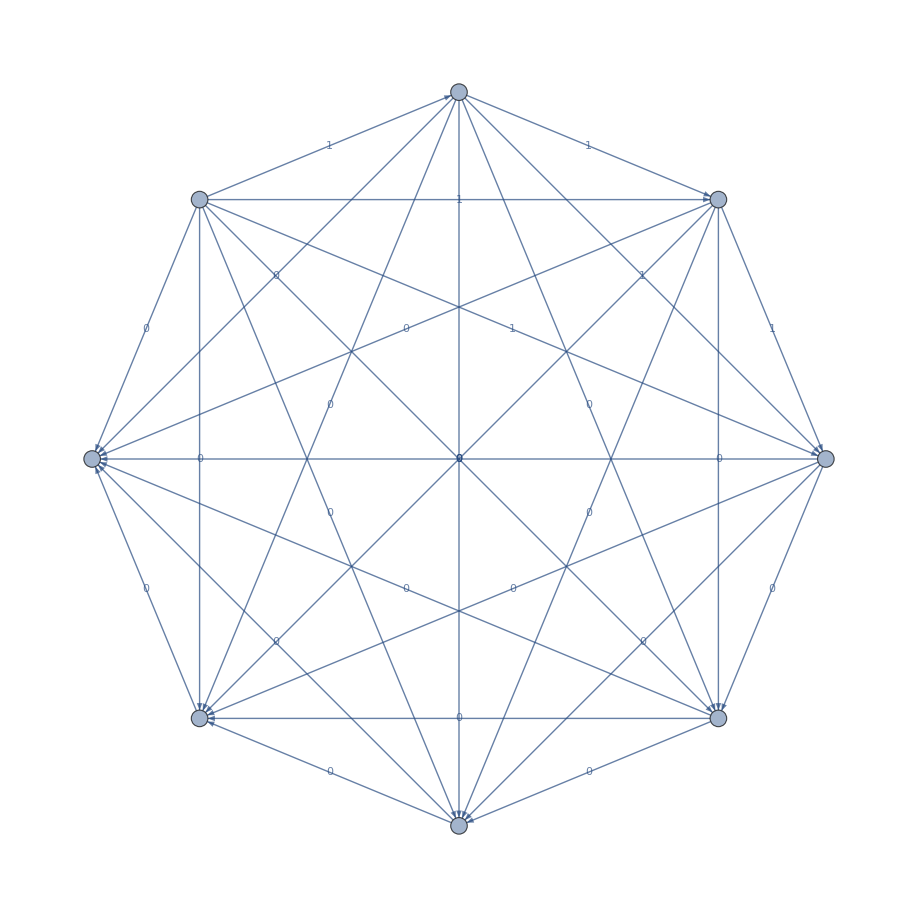

```mathematica
CellGraphEdges[cells_] := Flatten[Table[cells⟦i⟧-> cells⟦j⟧, {j, 1, Length[cells]},{i,1,j-1}],2]
CellGraph[ϕ_,weightsPositive_, weightsNegative_]:= Module[
{
cells =FormulaCells[ϕ],
edgeLabeling = (cell1_->cell2_):> (
(cell1->cell2) ->
RTerm[ϕ, cell1,cell2, weightsPositive, weightsNegative]),
vertexLabeling=cell↦(
cell ->{
STerm[ϕ, cell, weightsPositive, weightsNegative],
WTerm[ϕ, cell, weightsPositive, weightsNegative]})
},
With[
{edges= CellGraphEdges[cells]},
Graph[
edges,
EdgeLabels-> edges /. edgeLabeling,
VertexLabels->(vertexLabeling) /@ cells,
GraphLayout->"CircularEmbedding"
]
]
]
g=CellGraph[exampleDerangements,weightsPositiveDerangements,weightsNegativeDerangements]
```

```mathematica
(* Implementation of WFOMC according to formula (1) in Faster Lifting for Two-Variable Logic using Cell Graphs *)
OrderedPartitions[n_Integer,m_Integer]:= Flatten[
Permutations[PadRight[#,m]]&
/@IntegerPartitions[n,m],
1]
Pow[0,0]:=1
Pow[a_,b_]:=a^b
WFOMC1[ϕ_,n_,weightsPositive_, weightsNegative_]:= Module[{
s=STerms[ϕ, weightsPositiveDerangements, weightsNegativeDerangements],
w=WTerms[ϕ, weightsPositiveDerangements, weightsNegativeDerangements],
r=RTerms[ϕ, weightsPositiveDerangements, weightsNegativeDerangements],
u=2^(Length@PredicateSymbols[ϕ] ),
i,j},
Total[(partition |-> 
Multinomial[Sequence@@partition] *
Product[
r⟦i,j⟧~Pow~(partition⟦i⟧*partition⟦j⟧),
{j,1,u},
{i,1 , j-1}]*
Product[
s⟦i⟧~Pow~Binomial[partition⟦i⟧,2] *
 w⟦i⟧~Pow~partition⟦i⟧,
{i,1,u}]
) /@ OrderedPartitions[n, u]]
]
```

```mathematica
Table[
WFOMC1[
exampleDerangements,n,weightsPositiveDerangements,weightsNegativeDerangements],
 {n, 0, 5}]
```

{1,4,8,16,32,64}